```mathematica
μ=0.62;
γ=5/3;
```

```mathematica
years=365.25*86400;
tEnd=10^3 years;
```

```mathematica
rper=0.7Rsun;
θper=45*Pi/180;
kRoss=21.1;
χ=(16*T[Rper,zper]^3*sigmaSB)/(3*kRoss*ρ[Rper,zper]);  (*this is what MB call χ*)
ξradiative =(γ-1)/γ*T[Rper,zper]/P[Rper,zper]*χ     (*this is what MB call ξrad*)

ν=2.3   (*from Menou&Balbus2004*)

η=596     (*from Menou&Balbus2004*)


Timing[Table[θper=θ;
Timing[ListofSolutions=Table[Timing[

M=Random[Integer,{-12.5,-3.5}];
kRexp=Random[Real,{M-1.5,M+1.5}];
kϕexp=Random[Real,{M-1.5,M+1.5}];
kzexp=Random[Real,{M-1.5,M+1.5}];
kR0=(-1)^Random[Integer,{0,1}](2Pi)/(10^kRexp Rsun);
kϕ0=(-1)^Random[Integer,{0,1}](2Pi)/(10^kϕexp Rsun);
kz0=(-1)^Random[Integer,{0,1}](2Pi)/(10^kzexp Rsun);
kR[t_]=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]=kϕ0;
kz[t_]=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;

vSqmod0=vR0^2+vz0^2;
SolveTheSystem;
vSqmod[t_]=δvRsol[t]^2+δvzsol[t]^2;
MaxVelocitySq=(Max[vSqmod[tEnd/10^6],vSqmod[tEnd/10^5],vSqmod[tEnd/10^4],vSqmod[tEnd/10^3],vSqmod[tEnd/10^2],vSqmod[tEnd/10^1],vSqmod[tEnd]])/vSqmod0;
{kR0,kϕ0,kz0,MaxVelocitySq}],{q,1,10^2}];

ListofSolutions={θ,Sort[ListofSolutions, #1[[2]][[4]] > #2[[2]][[4]] &]};
PutAppend[ListofSolutions,"C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\RandomWavevectorTests\\Model A\\Model A - 3 - No Magnetic Field, Smaller Viscosity\\Model A 3 - Results.txt"];PutAppend[ListofSolutions[[2]][[1]][[2]],"C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\RandomWavevectorTests\\Model A\\Model A - 3 - No Magnetic Field, Smaller Viscosity\\Model A 3 - Short Results.txt"]],{θ,5/180 Pi,85/180 Pi,10/180 Pi}]]
```

1.42619×10^7

2.3

596

$Aborted

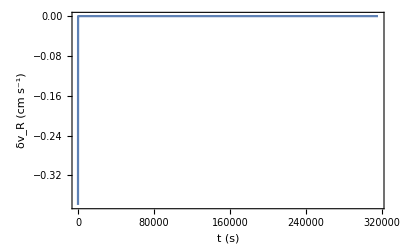

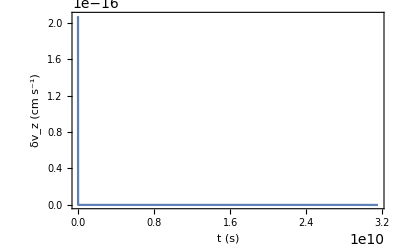

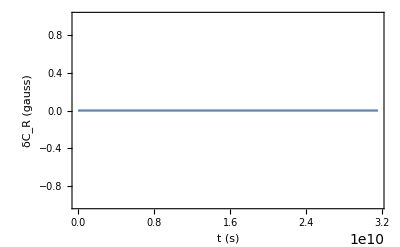

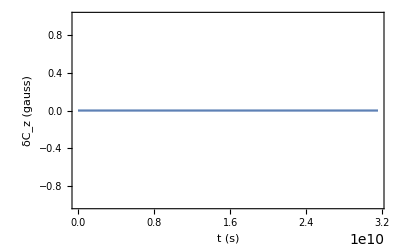

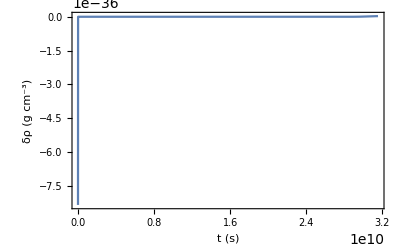

```mathematica
Plot[δvRsol[t],{t,0,tEnd/100000},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δv_R (cm s^-1)","Test 08 - δv_R(t)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
Plot[δvzsol[t],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δv_z (cm s^-1)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
Plot[δCRsol[t],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δC_R (gauss)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
Plot[δCzsol[t],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δC_z (gauss)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
Plot[δρsol[t],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δρ (g cm^-3)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
```